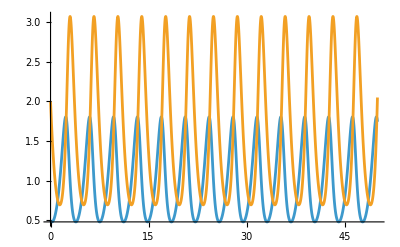

```mathematica
a= 1.6;b= 1.;c= 2.;d= 2;
sol=NDSolve[{x'[t]==a x[t]-b x[t] y[t],y'[t]==c x[t] y[t]-d y[t],x[0]==0.5,y[0]==2},{x[t],y[t]},{t,0,50}];
Plot[Evaluate[{{x[t],y[t]}/. sol}],{t,0,50},PlotRange->All]
```

```mathematica
(*Parameters*)γ=1;           (*Decay rate*)
Ω0=2;          (*Rabi frequency amplitude*)
ω=1;           (*Frequency of time-dependent driving*)

(*Time-dependent Hamiltonian*)
H[t_]:={{-I γ/2,-Ω0 Sin[ω t]},{-Ω0 Sin[ω t],0}};

(*Initial state:ground state*)
ψ0={1,0};

(*Time-dependent Schrödinger equation*)
eqns={I D[ψ[1][t],t]==H[t][[1,1]] ψ[1][t]+H[t][[1,2]] ψ[2][t],I D[ψ[2][t],t]==H[t][[2,1]] ψ[1][t]+H[t][[2,2]] ψ[2][t],ψ[1][0]==ψ0[[1]],ψ[2][0]==ψ0[[2]]};

(*Solve numerically*)
sol=NDSolveValue[eqns,{ψ[1],ψ[2]},{t,0,200}];

(*Plot population of each state over time*)
Plot[{Abs[sol[1][t]]^2,Abs[sol[2][t]]^2},{t,0,0.20},PlotLegends->{"Excited State","Ground State"},PlotLabel->"Population Dynamics of Two-Level Decaying System",AxesLabel->{"Time","Population"}]
```

-Graphics-

```mathematica
A={{0,0,1},{0,1, 0},{1,0,0}};
Inverse[A]
```

{{0,0,1},{0,1,0},{1,0,0}}

```mathematica
A.A
```

{{1,0,0},{0,1,0},{0,0,1}}

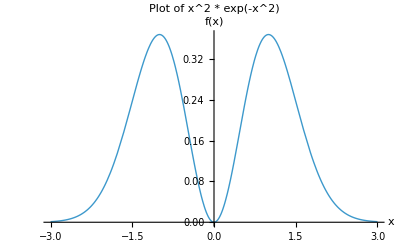

```mathematica
Plot[x^2 Exp[-x^2],{x,-3,3},PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"Plot of x^2 * exp(-x^2)",PlotStyle->Thick]
```

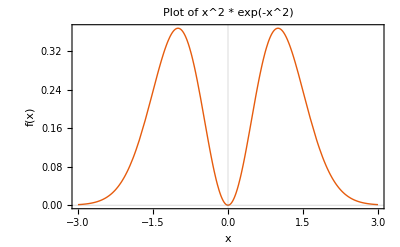

```mathematica
Plot[x^2 Exp[-x^2],{x,-3,3},PlotTheme->"Scientific",PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"Plot of x^2 * exp(-x^2)",PlotStyle->Thickness[Large]]
```

```mathematica
(*Define parameters as symbols or assign numerical values*)d12=Symbol["d12"];          (*Transition dipole moment*)
Delta=Symbol["Delta"];      (*Detuning parameter*)
Delta13=Symbol["Delta13"];  (*Another detuning parameter*)
omegaL2=Symbol["omegaL2"];  (*Laser frequency*)
Gamma=Symbol["Gamma"];      (*Decay rate*)
EnL2=Symbol["EnL2"];      (*Electric field amplitude*)
Omega13=Symbol["Omega13"];  (*Rabi frequency*)

(*Define the effective non-Hermitian Hamiltonian as a constant matrix*)
H={{0,d12,Omega13},{d12,Delta,0},{Omega13,0,Delta13-I*Gamma/2}};

(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[H];

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
```

Set::wrsym: Symbol Gamma is Protected.

Eigenvalues: {1/2 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,1],1/2 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,2],1/2 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,3]}

Eigenvectors: {{-1/(2 Omega13)(2 Delta13-ⅈ Gamma-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,1]),-1/(4 d12 Omega13)(4 Omega13^2+2 Delta13 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,1]-ⅈ Gamma Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,1]-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,1]^2),1},{-1/(2 Omega13)(2 Delta13-ⅈ Gamma-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,2]),-1/(4 d12 Omega13)(4 Omega13^2+2 Delta13 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,2]-ⅈ Gamma Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,2]-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,2]^2),1},{-1/(2 Omega13)(2 Delta13-ⅈ Gamma-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,3]),-1/(4 d12 Omega13)(4 Omega13^2+2 Delta13 Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,3]-ⅈ Gamma Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,3]-Root[8 d12^2 Delta13-4 ⅈ d12^2 Gamma+8 Delta Omega13^2+(-4 d12^2+4 Delta Delta13-2 ⅈ Delta Gamma-4 Omega13^2) #1+(-2 Delta-2 Delta13+ⅈ Gamma) #1^2+#1^3&,3]^2),1}}

```mathematica
B={{0,1},{1,-z}}
{eigenvalues,eigenvectors}=Eigensystem[B];
Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
```

{{0,1},{1,-z}}

Eigenvalues: {1/2 (-z-√(4+z^2)),1/2 (-z+√(4+z^2))}

Eigenvectors: {{1/2 (z-√(4+z^2)),1},{1/2 (z+√(4+z^2)),1}}

```mathematica
{0.13783457392369936+0.6087585167814451 ⅈ,0.781290405980598+0. ⅈ}.{0.7812904059805978+0. ⅈ,-0.13783457392369922-0.6087585167814452 ⅈ}
```

9.71445×10^-17-1.66533×10^-16 ⅈ

```mathematica
(*Define the functions E_plus and E_minus*)Eplus[z_]:=(z+Sqrt[4+z^2])/2;
Eminus[z_]:=(z-Sqrt[4+z^2])/2;

(*Define a hue-based color function mapping the phase from-π to π into the range[0,1]*)
phaseColor[val_]:=Hue[(val+Pi)/(2 Pi)];

(*Create density plots for the argument (phase) of Eplus and Eminus*)
phasePlotPlus=DensityPlot[Arg[Eplus[x+I y]],{x,-5,5},{y,-5,5},ColorFunction->(phaseColor[#]&),ColorFunctionScaling->False,PlotLegends->Automatic,PlotLabel->"Phase of E₊(z)",FrameLabel->{"Re(z)","Im(z)"},ImageSize->Medium];

phasePlotMinus=DensityPlot[Arg[Eminus[x+I y]],{x,-5,5},{y,-5,5},ColorFunction->(phaseColor[#]&),ColorFunctionScaling->False,PlotLegends->Automatic,PlotLabel->"Phase of E₋(z)",FrameLabel->{"Re(z)","Im(z)"},ImageSize->Medium];

(*Display the two plots side by side*)
GraphicsRow[{phasePlotPlus,phasePlotMinus}]
```

-Graphics-

```mathematica
(*Define the two branches of the function*)Eplus[z_]:=(z+Sqrt[4+z^2])/2;
Eminus[z_]:=(z-Sqrt[4+z^2])/2;

(*Plot the real part of Eplus(z) for z=x+I y*)
plotEplus=Plot3D[Re[Eplus[x+I y]],{x,-1,1},{y,-4,4},PlotLabel->"Real Part of E₊(z)",AxesLabel->{"Re(z)","Im(z)","Re(E₊)"},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->None,PlotRange->All];

(*Plot the real part of Eminus(z) for z=x+I y*)
plotEminus=Plot3D[Re[Eminus[x+I y]],{x,-1,1},{y,-4,4},PlotLabel->"Real Part of E₋(z)",AxesLabel->{"Re(z)","Im(z)","Re(E₋)"},ColorFunction->"Rainbow",ColorFunctionScaling->True,Mesh->None,PlotRange->All];x

(*Display the two plots side by side*)
GraphicsRow[{plotEplus,plotEminus}]
```

-Graphics-

```mathematica
Show[%214,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

-Graphics-

```mathematica
(*Define the two branches*)Eplus[z_]:=(z+Sqrt[4+z^2])/2;
Eminus[z_]:=(z-Sqrt[4+z^2])/2;

(*Create the 3D plot for E₊(z) with a blue color*)
plotEplus=Plot3D[Re[Eplus[x+I y]],{x,-1,1},{y,0,4},PlotStyle->Directive[Blue,Opacity[0.7]],Mesh->None,PlotRange->All,AxesLabel->{"Re(z)","Im(z)","Re(E)"}];

(*Create the 3D plot for E₋(z) with a red color*)
plotEminus=Plot3D[Re[Eminus[x+I y]],{x,-1,1},{y,0,4},PlotStyle->Directive[Red,Opacity[0.7]],Mesh->None,PlotRange->All];

(*Combine the two plots into a single graph*)
Show[plotEplus,plotEminus,PlotLabel->"Real Part of E₊(z) (blue) and E₋(z) (red)",BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Clear[z]
(*Define the eigenvector components*)
v1={1/2 (z-Sqrt[4+z^2]),1};
v2={1/2 (z+Sqrt[4+z^2]),1};

(*Expand the first component around z=-2 I up to order 3 (i.e.including terms up to (z+2i)^(3/2))*)
seriesV1=Series[v1[[1]],{z,-2 I,1}]//Normal;
seriesV2=Series[v2[[1]],{z,-2 I,1}]//Normal;

Print["Expansion of eigenvector 1 (first component): ",seriesV1];
Print["Expansion of eigenvector 2 (first component): ",seriesV2];
```

Expansion of eigenvector 1 (first component): -ⅈ-√(2-ⅈ z)+1/2 (2 ⅈ+z)

Expansion of eigenvector 2 (first component): -ⅈ+√(2-ⅈ z)+1/2 (2 ⅈ+z)

```mathematica
(*Clear any previous definitions*)ClearAll[a,b,c,d,e,f,g,h,i,M]

(*Define a general 3x3 matrix with complex entries*)
M={{0,a,b},{a,c,0},{b,0,d-I*g}};

(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[M];

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];

(*Compute the characteristic polynomial p(λ)=Det(M-λ I)*)charPoly=Expand[Det[M-lambda IdentityMatrix[3]]];
Print["Characteristic polynomial: ",charPoly];

(*Compute the discriminant of the characteristic polynomial with respect to λ*)
disc=Factor[Discriminant[charPoly,lambda]];
Print["Discriminant: ",disc];

(*The eigenvalues (and hence the eigenvectors) degenerate when the discriminant equals zero.That is,the condition for degeneracy is:*)
degeneracyCondition=disc==0;
Print["Degeneracy condition (eigenvalue/eigenvector degeneracy): ",degeneracyCondition];
```

Eigenvalues: {Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,1],Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,2],Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,3]}

Eigenvectors: {{-(d-ⅈ g-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,1])/b,-1/(a b)(b^2+d Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,1]-ⅈ g Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,1]-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,1]^2),1},{-(d-ⅈ g-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,2])/b,-1/(a b)(b^2+d Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,2]-ⅈ g Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,2]-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,2]^2),1},{-(d-ⅈ g-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,3])/b,-1/(a b)(b^2+d Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,3]-ⅈ g Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,3]-Root[b^2 c+a^2 d-ⅈ a^2 g+(-a^2-b^2+c d-ⅈ c g) #1+(-c-d+ⅈ g) #1^2+#1^3&,3]^2),1}}

Characteristic polynomial: -b^2 c-a^2 d+ⅈ a^2 g+a^2 lambda+b^2 lambda-c d lambda+ⅈ c g lambda+c lambda^2+d lambda^2-ⅈ g lambda^2-lambda^3

Discriminant: 4 a^6+12 a^4 b^2+12 a^2 b^4+4 b^6+a^4 c^2+20 a^2 b^2 c^2-8 b^4 c^2+4 b^2 c^4+8 a^4 c d-38 a^2 b^2 c d+8 b^4 c d+2 a^2 c^3 d-8 b^2 c^3 d-8 a^4 d^2+20 a^2 b^2 d^2+b^4 d^2+2 a^2 c^2 d^2+2 b^2 c^2 d^2+c^4 d^2-8 a^2 c d^3+2 b^2 c d^3-2 c^3 d^3+4 a^2 d^4+c^2 d^4-8 ⅈ a^4 c g+38 ⅈ a^2 b^2 c g-8 ⅈ b^4 c g-2 ⅈ a^2 c^3 g+8 ⅈ b^2 c^3 g+16 ⅈ a^4 d g-40 ⅈ a^2 b^2 d g-2 ⅈ b^4 d g-4 ⅈ a^2 c^2 d g-4 ⅈ b^2 c^2 d g-2 ⅈ c^4 d g+24 ⅈ a^2 c d^2 g-6 ⅈ b^2 c d^2 g+6 ⅈ c^3 d^2 g-16 ⅈ a^2 d^3 g-4 ⅈ c^2 d^3 g+8 a^4 g^2-20 a^2 b^2 g^2-b^4 g^2-2 a^2 c^2 g^2-2 b^2 c^2 g^2-c^4 g^2+24 a^2 c d g^2-6 b^2 c d g^2+6 c^3 d g^2-24 a^2 d^2 g^2-6 c^2 d^2 g^2-8 ⅈ a^2 c g^3+2 ⅈ b^2 c g^3-2 ⅈ c^3 g^3+16 ⅈ a^2 d g^3+4 ⅈ c^2 d g^3+4 a^2 g^4+c^2 g^4

Degeneracy condition (eigenvalue/eigenvector degeneracy): 4 a^6+12 a^4 b^2+12 a^2 b^4+4 b^6+a^4 c^2+20 a^2 b^2 c^2-8 b^4 c^2+4 b^2 c^4+8 a^4 c d-38 a^2 b^2 c d+8 b^4 c d+2 a^2 c^3 d-8 b^2 c^3 d-8 a^4 d^2+20 a^2 b^2 d^2+b^4 d^2+2 a^2 c^2 d^2+2 b^2 c^2 d^2+c^4 d^2-8 a^2 c d^3+2 b^2 c d^3-2 c^3 d^3+4 a^2 d^4+c^2 d^4-8 ⅈ a^4 c g+38 ⅈ a^2 b^2 c g-8 ⅈ b^4 c g-2 ⅈ a^2 c^3 g+8 ⅈ b^2 c^3 g+16 ⅈ a^4 d g-40 ⅈ a^2 b^2 d g-2 ⅈ b^4 d g-4 ⅈ a^2 c^2 d g-4 ⅈ b^2 c^2 d g-2 ⅈ c^4 d g+24 ⅈ a^2 c d^2 g-6 ⅈ b^2 c d^2 g+6 ⅈ c^3 d^2 g-16 ⅈ a^2 d^3 g-4 ⅈ c^2 d^3 g+8 a^4 g^2-20 a^2 b^2 g^2-b^4 g^2-2 a^2 c^2 g^2-2 b^2 c^2 g^2-c^4 g^2+24 a^2 c d g^2-6 b^2 c d g^2+6 c^3 d g^2-24 a^2 d^2 g^2-6 c^2 d^2 g^2-8 ⅈ a^2 c g^3+2 ⅈ b^2 c g^3-2 ⅈ c^3 g^3+16 ⅈ a^2 d g^3+4 ⅈ c^2 d g^3+4 a^2 g^4+c^2 g^4==0

```mathematica
ClearAll["Global`*"]

(*Set parameter values*)
Delta2=1;
gam=1;  (*using gam instead of Gamma*)
z=Delta2-I*gam/2;

(*Define the eigenvalue functions as a function of ω,where ω is complex*)
Eplus[omega_]:=(z+Sqrt[z^2+4 omega^2])/2;
Eminus[omega_]:=(z-Sqrt[z^2+4 omega^2])/2;

(*Plot for E₊:real part*)
plotEplusReal=Plot3D[Re[Eplus[x+I y]],{x,-1,1},{y,-1,1},PlotLabel->"Re[E₊(Ω)]",AxesLabel->{"Re(Ω)","Im(Ω)","Re(E₊)"},ColorFunction->"Rainbow",Mesh->None,PlotRange->All];

(*Plot for E₊:imaginary part*)
plotEplusImag=Plot3D[Im[Eplus[x+I y]],{x,-1,1},{y,-1,1},PlotLabel->"Im[E₊(Ω)]",AxesLabel->{"Re(Ω)","Im(Ω)","Im(E₊)"},ColorFunction->"Rainbow",Mesh->None,PlotRange->All];

(*Plot for E₋:real part*)
plotEminusReal=Plot3D[Re[Eminus[x+I y]],{x,-1,1},{y,-1,1},PlotLabel->"Re[E₋(Ω)]",AxesLabel->{"Re(Ω)","Im(Ω)","Re(E₋)"},ColorFunction->"Rainbow",Mesh->None,PlotRange->All];

(*Plot for E₋:imaginary part*)
plotEminusImag=Plot3D[Im[Eminus[x+I y]],{x,-1,1},{y,-1,1},PlotLabel->"Im[E₋(Ω)]",AxesLabel->{"Re(Ω)","Im(Ω)","Im(E₋)"},ColorFunction->"Rainbow",Mesh->None,PlotRange->All];

(*Arrange the plots in a grid*)
GraphicsGrid[{{plotEplusReal,plotEplusImag},{plotEminusReal,plotEminusImag}}]
```

-Graphics-

```mathematica
Show[plotEplusReal,plotEminusReal,PlotLabel->"Real Part of E₊(z) (blue) and E₋(z) (red)",BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Show[plotEplusImag,plotEminusImag,PlotLabel->"Real Part of E₊(z) (blue) and E₋(z) (red)",BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"]
(*Define a general 3x3 matrix with complex entries*)
M={{0,x},{x,z}};

(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[M];

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
```

Eigenvalues: {1/2 (z-√(4 x^2+z^2)),1/2 (z+√(4 x^2+z^2))}

Eigenvectors: {{-(z+√(4 x^2+z^2))/(2 x),1},{-(z-√(4 x^2+z^2))/(2 x),1}}

Eigenvalues at x = 1: {ⅈ,ⅈ}

Eigenvectors at x = 1: {{-ⅈ,1},{0,0}}

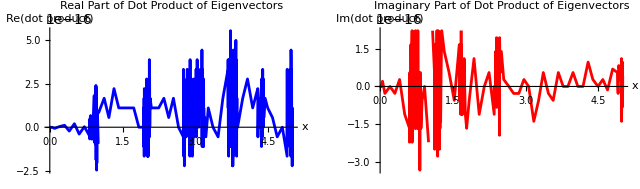

```mathematica
ClearAll["Global`*"]

(*Let z be a general complex constant,e.g.,2+3 I.You can change this as desired.*)
z=2* I;

(*Define the 2x2 matrix as a function of x*)
M[x_]:={{0,x},{x,z}};

(*Compute the eigenvalues and eigenvectors for the matrix M[x]*)
eigensystem[x_]:=Eigensystem[M[x]];

(*Define a function to compute the dot product of the two eigenvectors.(Here we use the standard dot product.For a Hermitian inner product,one would use Conjugate[vec1].vec2.)*)
dotProduct[x_]:=Module[{vals,vecs},{vals,vecs}=eigensystem[x];
vecs[[1]].vecs[[2]]];

(*Print eigenvalues and eigenvectors for a sample value of x (say,x=1)*)
{valsSample,vecsSample}=eigensystem[1];
Print["Eigenvalues at x = 1: ",valsSample];
Print["Eigenvectors at x = 1: ",vecsSample];

(*Now,plot the real and imaginary parts of the dot product as a function of x*)
plotDotReal=Plot[Re[dotProduct[x]],{x,0,5},PlotLabel->"Real Part of Dot Product of Eigenvectors",AxesLabel->{"x","Re(dot product)"},PlotStyle->Blue];

plotDotImag=Plot[Im[dotProduct[x]],{x,0,5},PlotLabel->"Imaginary Part of Dot Product of Eigenvectors",AxesLabel->{"x","Im(dot product)"},PlotStyle->Red];

GraphicsRow[{plotDotReal,plotDotImag}]
```

```mathematica
(*Full process for verification*)H={{0,x[t]},{x[t],z}};

(*Right eigenvectors*)
{valsR,vecsR}=Eigensystem[H];

(*Left eigenvectors*)
{valsL,vecsL}=Eigensystem[ConjugateTranspose[H]];

(*Normalization*)
vecsRnorm=Normalize/@vecsR;
vecsLnorm=Normalize/@vecsL;

(*Biorthonormality check*)
Table[Conjugate[vecsLnorm[[i]]].vecsRnorm[[j]],{i,Length[vecsLnorm]},{j,Length[vecsRnorm]}]//MatrixForm
```

(Conjugate[1/(√(1+Abs[(-ⅈ+√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+Abs[(ⅈ+√(-1+x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+Abs[(-ⅈ+√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (ⅈ+Conjugate[√(-1+Conjugate[x[t]]^2)]) (ⅈ+√(-1+x[t]^2)))/(√(1+Abs[(ⅈ+√(-1+x[t]^2))/x[t]]^2) x[t]^2) | Conjugate[1/(√(1+Abs[(-ⅈ+√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+Abs[(ⅈ-√(-1+x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+Abs[(-ⅈ+√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (ⅈ+Conjugate[√(-1+Conjugate[x[t]]^2)]) (ⅈ-√(-1+x[t]^2)))/(√(1+Abs[(ⅈ-√(-1+x[t]^2))/x[t]]^2) x[t]^2)
Conjugate[1/(√(1+Abs[(-ⅈ-√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+Abs[(ⅈ+√(-1+x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+Abs[(-ⅈ-√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (ⅈ-Conjugate[√(-1+Conjugate[x[t]]^2)]) (ⅈ+√(-1+x[t]^2)))/(√(1+Abs[(ⅈ+√(-1+x[t]^2))/x[t]]^2) x[t]^2) | Conjugate[1/(√(1+Abs[(-ⅈ-√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+Abs[(ⅈ-√(-1+x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+Abs[(-ⅈ-√(-1+Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (ⅈ-Conjugate[√(-1+Conjugate[x[t]]^2)]) (ⅈ-√(-1+x[t]^2)))/(√(1+Abs[(ⅈ-√(-1+x[t]^2))/x[t]]^2) x[t]^2))

```mathematica
(*Define variables*)
Clear[x,z,t]
H={{0,x[t]},{x[t],z}};
(*Compute eigenvalues and right eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[H]
(*Compute left eigenvectors by taking Eigensystem of the conjugate transpose*){leftEigenvalues,leftEigenvectors}=Eigensystem[ConjugateTranspose[H]]
(*The eigenvectors might not be normalized by default*)

(*Normalize right eigenvectors*)
normalizedRightEigenvectors=Normalize/@eigenvectors;
(*Normalize left eigenvectors*)
normalizedLeftEigenvectors=Normalize/@leftEigenvectors;
(*Compute the inner product between left and right eigenvectors*)
innerProductMatrix=Table[ConjugateTranspose[normalizedLeftEigenvectors[[i]]].normalizedRightEigenvectors[[j]],{i,Length[normalizedLeftEigenvectors]},{j,Length[normalizedRightEigenvectors]}];

(*Display the result*)
MatrixForm[innerProductMatrix]
(*Substitute example values for x(t) and z*)exampleResult=N[innerProductMatrix/. {x[t]->1,z->2*I}]
MatrixForm[exampleResult]
```

{{1/2 (z-√(z^2+4 x[t]^2)),1/2 (z+√(z^2+4 x[t]^2))},{{-(z+√(z^2+4 x[t]^2))/(2 x[t]),1},{-(z-√(z^2+4 x[t]^2))/(2 x[t]),1}}}

{{1/2 (Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2)),1/2 (Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))},{{-(Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/(2 Conjugate[x[t]]),1},{-(Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/(2 Conjugate[x[t]]),1}}}

(Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+1/4 Abs[(z+√(z^2+4 x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (z+Conjugate[√(Conjugate[z]^2+4 Conjugate[x[t]]^2)]) (z+√(z^2+4 x[t]^2)))/(4 √(1+1/4 Abs[(z+√(z^2+4 x[t]^2))/x[t]]^2) x[t]^2) | Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+1/4 Abs[(z-√(z^2+4 x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]+√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (z+Conjugate[√(Conjugate[z]^2+4 Conjugate[x[t]]^2)]) (z-√(z^2+4 x[t]^2)))/(4 √(1+1/4 Abs[(z-√(z^2+4 x[t]^2))/x[t]]^2) x[t]^2)
Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+1/4 Abs[(z+√(z^2+4 x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (z-Conjugate[√(Conjugate[z]^2+4 Conjugate[x[t]]^2)]) (z+√(z^2+4 x[t]^2)))/(4 √(1+1/4 Abs[(z+√(z^2+4 x[t]^2))/x[t]]^2) x[t]^2) | Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))]/(√(1+1/4 Abs[(z-√(z^2+4 x[t]^2))/x[t]]^2))+(Conjugate[1/(√(1+1/4 Abs[(Conjugate[z]-√(Conjugate[z]^2+4 Conjugate[x[t]]^2))/Conjugate[x[t]]]^2))] (z-Conjugate[√(Conjugate[z]^2+4 Conjugate[x[t]]^2)]) (z-√(z^2+4 x[t]^2)))/(4 √(1+1/4 Abs[(z-√(z^2+4 x[t]^2))/x[t]]^2) x[t]^2))

{{0.,0.},{0.,0.}}

(0. | 0.
0. | 0.)

```mathematica
ClearAll["Global`*"]
(*Define a general 3x3 matrix with complex entries*)
a = 1;
M={{0,a},{a,z}};

(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[M];
{leftEigenvalues,leftEigenvectors}=Eigensystem[ConjugateTranspose[M]];

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
```

Eigenvalues: {1/2 (z-√(4+z^2)),1/2 (z+√(4+z^2))}

Eigenvectors: {{1/2 (-z-√(4+z^2)),1},{1/2 (-z+√(4+z^2)),1}}

```mathematica
a=1;
M={{0,a},{a,z}};

(*1) Compute the right and left eigenvalues/eigenvectors*)
{valsR,vecsR}=Eigensystem[M];
{valsL,vecsL}=Eigensystem[ConjugateTranspose[M]];

(*2) Print normalized eigenvectors*)
Do[Module[{vR,vL,overlap,normR,normL},vR=vecsR[[i]];
vL=vecsL[[i]];
(*3) Compute the overlap and normalize*)overlap=ConjugateTranspose[vL].vR;
normR=vR/Sqrt[overlap];
normL=vL/Sqrt[Conjugate[overlap]];
(*4) Print results*)Print["Eigenvalue: ",valsR[[i]]];
Print["  Normalized Right vector: ",normR];
Print["  Normalized Left vector:  ",normL];
Print["-----------------------------------"];],{i,1,Length[valsR]}];
```

Eigenvalue: 1/2 (z-√(4+z^2))

Normalized Right vector: {(-z-√(4+z^2))/(2 √(1+1/4 (-z-√(4+z^2)) (-z-Conjugate[√(4+Conjugate[z]^2)]))),1/(√(1+1/4 (-z-√(4+z^2)) (-z-Conjugate[√(4+Conjugate[z]^2)])))}

Normalized Left vector:  {(-Conjugate[z]-√(4+Conjugate[z]^2))/(2 √(1+1/4 (-Conjugate[z]-√(4+Conjugate[z]^2)) (-Conjugate[z]-Conjugate[√(4+z^2)]))),1/(√(1+1/4 (-Conjugate[z]-√(4+Conjugate[z]^2)) (-Conjugate[z]-Conjugate[√(4+z^2)])))}

-----------------------------------

Eigenvalue: 1/2 (z+√(4+z^2))

Normalized Right vector: {(-z+√(4+z^2))/(2 √(1+1/4 (-z+√(4+z^2)) (-z+Conjugate[√(4+Conjugate[z]^2)]))),1/(√(1+1/4 (-z+√(4+z^2)) (-z+Conjugate[√(4+Conjugate[z]^2)])))}

Normalized Left vector:  {(-Conjugate[z]+√(4+Conjugate[z]^2))/(2 √(1+1/4 (-Conjugate[z]+√(4+Conjugate[z]^2)) (-Conjugate[z]+Conjugate[√(4+z^2)]))),1/(√(1+1/4 (-Conjugate[z]+√(4+Conjugate[z]^2)) (-Conjugate[z]+Conjugate[√(4+z^2)])))}

-----------------------------------

Syntax::stresc: Unknown string escape \u.

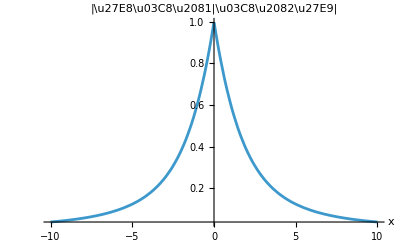

```mathematica
ClearAll["Global`*"]
(*Define M as a function of real parameter x,so that z=-2 I+x.*)
M[x_]:={{0,1},{1,-2 I+x}};

(*Define a function that returns the overlap between the two right eigenvectors of M[x].*)
overlapOfEigenvectors[x_]:=Module[{vals,vecs,ov},(*Get eigenvalues and (right) eigenvectors of M[x].*){vals,vecs}=Eigensystem[M[x]];
(*In Mathematica,vecs[[1]] and vecs[[2]] are column vectors.The usual “bra-ket” overlap is v1^\dagger v2,which is ConjugateTranspose[v1].v2 in Mathematica.*)ov=ConjugateTranspose[vecs[[1]]].vecs[[2]];
(*Return that overlap.*)ov];
Plot[Abs[overlapOfEigenvectors[x]],{x,-10,10},PlotRange->All,AxesLabel->{"x","|\u27E8\u03C8\u2081|\u03C8\u2082\u27E9|"}]
```

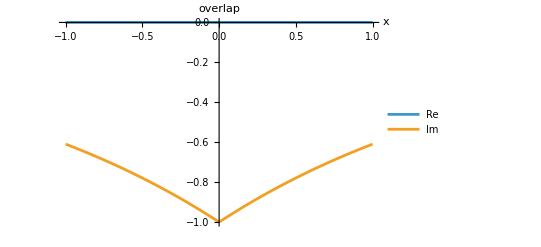

```mathematica
Plot[{Re[overlapOfEigenvectors[x]],Im[overlapOfEigenvectors[x]]},{x,-1,1},PlotRange->All,PlotLegends->{"Re","Im"},AxesLabel->{"x","overlap"}]
```

```mathematica
(*Define a function that computes the overlap for a given deviation δ=x+i y*)overlap[x_,y_]:=Module[{mat,vals,vecs,ov},(*z=-2I+δ*)mat={{0,1},{1,-2 I+(x+I y)}};
(*Compute right eigenvalues and eigenvectors*){vals,vecs}=Eigensystem[mat];
(*Compute the overlap between the two eigenvectors*)ov=ConjugateTranspose[vecs[[1]]].vecs[[2]];
ov];

(*Plot the absolute value of the overlap in 3D*)
Plot3D[Abs[overlap[x,y]],{x,-5,5},{y,-5,5},AxesLabel->{"Re(δ)","Im(δ)","|Overlap|"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"Absolute Overlap vs. Deviation δ (with z = -2i + δ)"]
```

-Graphics3D-

```mathematica
(*Define parameters*)x[z_]:=1;
zList=Table[2 I+0.1 Exp[I t],{t,0,2 Pi,2 Pi/20}];

(*Define eigenvectors*)
RightEigenvector1[z_]:=Normalize[{-((z+Sqrt[z^2+4 x[z]^2])/(2 x[z])),1}];
RightEigenvector2[z_]:=Normalize[{-((z-Sqrt[z^2+4 x[z]^2])/(2 x[z])),1}];

LeftEigenvector1[z_]:=Conjugate[RightEigenvector1[z]];
LeftEigenvector2[z_]:=Conjugate[RightEigenvector2[z]];

(*Overlap matrix for each step*)
M[z1_,z2_]:={{Conjugate[LeftEigenvector1[z1]].RightEigenvector1[z2],Conjugate[LeftEigenvector1[z1]].RightEigenvector2[z2]},{Conjugate[LeftEigenvector2[z1]].RightEigenvector1[z2],Conjugate[LeftEigenvector2[z1]].RightEigenvector2[z2]}};

(*Compute U matrix*)
U=Fold[Dot,IdentityMatrix[2],Table[M[zList[[i]],zList[[i+1]]],{i,Length[zList]-1}]];

(*Extract total Berry phase*)
theta=-Im[Log[Det[U]]]

(*Display U*)
MatrixForm[U]
```

-3.14159

(-1.3852×10^-12-3.40254×10^-14 ⅈ | 5.81791×10^-11-1.83207×10^-11 ⅈ
5.82011×10^-11+1.8326×10^-11 ⅈ | 1.3852×10^-12+3.40254×10^-14 ⅈ)

```mathematica
ClearAll["Global`*"]

(*Define the eigenvalue functions for the 2×2 Hamiltonian*)
Eplus[z_,x_]:=(z+Sqrt[x^2+z^2])/2;
Eminus[z_,x_]:=(z-Sqrt[x^2+z^2])/2;

(*In our case,we set gam=0 so that z=Δ₂ is real.We will let d denote Δ₂ and x denote Ω.*)
(*Define the mixing (ground state projection) for each eigenstate*)
mixingEplus[d_,x_]:=(1-d/Sqrt[d^2+4 x^2])/2;
mixingEminus[d_,x_]:=(1+d/Sqrt[d^2+4 x^2])/2;

(*Plot settings:note that the ranges below are as given in your code;
they are quite large,so adjust if necessary.*)

plotEplus=Plot3D[Re[Eplus[d,x]],{d,-3*10^6*2*Pi,3*10^6*2*Pi},{x,-2*10^7,2*10^7},PlotRange->All,PlotStyle->Directive[Opacity[0.8]],ColorFunction->Function[{d,x,z},ColorData["Rainbow"][mixingEplus[d,x]]],ColorFunctionScaling->False,Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral",Axes->True,AxesLabel->{Subscript["Δ",2]<>" (rad/s)","Ω (rad/s)","Re(E)"},AxesStyle->Thick,BoxRatios->{1,1,1},PlotLegends->BarLegend[{ColorData["Rainbow"],{-1,1}},LabelStyle->{Bold,12},LegendLabel->"Mixing"]];

plotEminus=Plot3D[Re[Eminus[d,x]],{d,-3*10^6*2*Pi,3*10^6*2*Pi},{x,-2*10^7,2*10^7},PlotRange->All,PlotStyle->Directive[Opacity[0.8]],ColorFunction->Function[{d,x,z},ColorData["Rainbow"][mixingEminus[d,x]]],ColorFunctionScaling->False,Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral",Axes->True,AxesLabel->{Subscript["Δ",2]<>" (rad/s)","Ω (rad/s)","Re(E\!$begin:math:text$\\[PlusMinus]$end:math:text$)"},AxesStyle->Thick,BoxRatios->{1,1,1}];

(*Combine the two surfaces into one 3D view*)
Show[plotEplus,plotEminus]
```

StringJoin::string: String expected at position 1 in Δ_2<> (rad/s).

-Graphics3D-

```mathematica
M={{0,g},{g,-I 2 g}};

(*Compute the eigenvalues and eigenvectors*)
{eigenvalues,eigenvectors}=Eigensystem[M];

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
```

Eigenvalues: {-ⅈ g,-ⅈ g}

Eigenvectors: {{ⅈ,1},{0,0}}